# Total Aberrations

```mathematica
Off[General::spell1]
Off[General::spell]
Off[∞::indet]
Off[Power::infy]
Off[Simplify::infd]

TotalAberrations[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,option1_]:=
Module[{},
(* number of surfaces and wave lengths *)
n=Length[rad];
m=Length[waves];

(* Distances among the surfaces *)
thicke=Reverse[Take[thick,{1,nstop-1}]];
thicke1=Join[thicke,{0}];
rade=-Reverse[Take[rad,{1,nstop}]]//Flatten;

(* Evaluation of the aperture stop images supplied by the surfaces preceeding the stop:
the last one is the entrance pupil. *)
Do[
inde[h]=Reverse[Take[ind[[h]],{1,nstop}]];
inde1[h]=Prepend[inde[h],1],
{h,1,m}];


Do[
ze[h,1]=If[nstop===0,dis,-dis],
{h,1,3}];

Do[
Do[
Qe[h,i]=(inde1[h][[i]])/ze[h,i]-(inde1[h][[i]])/rade[[i]]-(inde1[h][[i+1]])/w1[h,i]+(inde1[h][[i+1]])/rade[[i]];
ze1[h,i]=Which[ze[h,i]===0,ze[h,i],ze[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,ze[h,i]=!=-Infinity&&Simplify[Numerator[Together[(inde1[h][[i]])/ze[h,i]-(inde1[h][[i]])/rad[[i]]+(inde1[h][[i+1]])/rad[[i]]]]]===0,-Infinity,ze[h,i]=!=-Infinity||ze[h,i]===-Infinity,Solve[Qe[h,i]==0,w1[h,i]][[1,1,2]]]; ze[h,i+1]=ze1[h,i]-thicke1[[i]],
{i,1,nstop}],
{h,1,m}];
Do[
de[h]=Which[nstop===0,dis,nstop=!=0,-ze1[h,nstop]],
{h,1,3}];

If[option1==1,Print["Distance of entrance pupil from the first surface for λ = ",waves[[1]]]];
If[option1==1,Print["w_e = ", de[1](*//Simplify*)]];

Do[
ye[h,1]=stoprad;
Do[
ye1[h,i]=If[ze[h,i]=!=0,(inde1[h][[i]] ze1[h,i])/(inde1[h][[i+1]] ze[h,i])ye[h,i],ye[h,i]];
ye[h,i+1]=ye1[h,i],
{i,1,nstop}];
diame[h]=Which[nstop===0,stoprad,nstop=!=0,ye1[h,nstop]],
{h,1,m}];

If[option1==1,Print["Radius of entrance pupil for λ = ",waves[[1]]]];
If[option1==1,Print["r_en = ",diame[1]]];

(* Evaluation of exit pupil *)
thick2=Join[thick,{0}];
Do[
zee[h,1]=de[h];
Do[zee1[h,i]=Which[zee[h,i]===0,0,zee[h,i]===-Infinity&&Abs[rad[[i]]]===Infinity,-Infinity,zee[h,i]=!=-Infinity&&ind[[h,i]]/zee[h,i]-ind[[h,i]]/rad[[i]]+ind[[h,i+1]]/rad[[i]]===0,-Infinity,zee[h,i]=!=-Infinity||zee[h,i]===-Infinity,Solve[Numerator[Together[ind[[h,i]]/zee[h,i]-ind[[h,i]]/rad[[i]]-ind[[h,i+1]]/fe1[h,i]+ind[[h,i+1]]/rad[[i]]]]==0,fe1[h,i]][[1]][[1,2]]];zee[h,i+1]=zee1[h,i]-thick2[[i]],
{i,1,n}],{h,1,m}];

If[option1==1,Print["Distance of the exit pupil from the last surface for λ = ",waves[[1]]]];
If[option1==1,Print["w_(e, n) = ",zee1[1,n](*//Simplify*)]];

Do[
yee[h,1]=diame[h];
Do[
yee1[h,i]=Which[zee[h,i]=!=0,(ind[[h,i]] zee1[h,i])/(ind[[h,i+1]] zee[h,i])yee[h,i],zee[h,i]===0,yee[h,i]];
yee[h,i+1]=yee1[h,i],{i,1,n}],
{h,1,m}];

If[option1==1,Print["Radius of exit pupil for λ = ",waves[[1]]]];
If[option1==1,Print["r_ex = ",Abs[ yee1[1,n]]]];

(* Pupil Magnification  *)

Do[
Do[
Mae[h,i]=yee1[h,i]/yee[h,1],
{i,1,n}],
{h,1,m}];

(*Principal planes and focal length*)
Do[
Do[P[h,i]=(ind[[h,i+1]]-ind[[h,i]])/rad[[i]];
R0[h,i]={{1,0},{(-P[h,i])/ind[[h,i+1]],ind[[h,i]]/ind[[h,i+1]]}},
{i,1,n}],
{h,1,m}];


If[n==1,Goto[1],Goto[2]];

Label[1];
Do[Mt[h]=R0[h,1],{h,1,m}];

Goto[3];

Label[2];
(*Total matrix of the i-th surface*)

Do[D0[i]={{1,thick[[i]]},{0,1}},{i,1,n-1}];
Do[
Do[
B0[h,i]=If[i<n,D0[i].R0[h,i],R0[h,n]],{i,1,n}],{h,1,m}];

(*Matrices of the sub-systems*)
Do[
Do[
b[h,1]=B0[h,1];
b[h,i]=B0[h,i].b[h,i-1],
{i,2,n}],{h,1,m}];

(*Total matrix of the system*)
Do[Mt[h]=b[h,n],{h,1,m}];
Label[3];


(*Distances of the principal planes from the first and last surface, respectively*)


Do[
zp[h]=If[Mt[h][[2,1]]===0,0,1/(Mt[h][[2,1]])(Mt[h][[1,2]]Mt[h][[2,1]]+Mt[h][[2,2]]-Mt[h][[1,1]]Mt[h][[2,2]])];
z1p[h]=If[Mt[h][[2,1]]===0,0,(1-Mt[h][[1,1]])/(Mt[h][[2,1]])],{h,1,m}];
(***********************************)
If[option1===1,Print["Distance of the first principal plane from the first surface = ",zp[1]]];
If[option1===1,Print["Distance of the second principal plane from the last surface = ",z1p[1]]];

(* Distances of the images *)


Do[zog[h,1]=dobject,{h,1,m}];

Do[
Do[zog1[h,i]=Which[rad[[i]]=!=Infinity&&zog[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])]=!=ComplexInfinity,Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])],

rad[[i]]=!=Infinity&&zog[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zog[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zog[h,i]+ind[[h,i+1]] zog[h,i])]===ComplexInfinity,-Infinity,rad[[i]]===Infinity&&zog[h,i]=!=-Infinity,(ind[[h,i+1]]zog[h,i])/ind[[h,i]],rad[[i]]=!=Infinity&&zog[h,i]===-Infinity,(ind[[h,i+1]] rad[[i]])/(-ind[[h,i]]+ind[[h,i+1]]),rad[[i]]===Infinity&&zog[h,i]===-Infinity,-Infinity];zog[h,i+1]=zog1[h,i]-thick2[[i]],{i,1,n}],{h,1,m}];
If[option1==1,Print["Gaussian distances of the images from the surfaces for λ = ",waves[[1]]]];
If[option1==1,Print[Table[zog1[1,i],{i,1,n}]]];

(*Focal length *)
Do[zoginf[h,1]=-Infinity,{h,1,m}];
Do[
Do[zog1inf[h,i]=Which[rad[[i]]=!=Infinity&&zoginf[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])]=!=ComplexInfinity,Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])],

rad[[i]]=!=Infinity&&zoginf[h,i]=!=-Infinity&&Simplify[(ind[[h,i+1]] rad[[i]] zoginf[h,i])/(ind[[h,i]]rad[[i]]-ind[[h,i]]zoginf[h,i]+ind[[h,i+1]] zoginf[h,i])]===ComplexInfinity,-Infinity,rad[[i]]===Infinity&&zoginf[h,i]=!=-Infinity,(ind[[h,i+1]]zoginf[h,i])/ind[[h,i]],rad[[i]]=!=Infinity&&zoginf[h,i]===-Infinity,(ind[[h,i+1]] rad[[i]])/(-ind[[h,i]]+ind[[h,i+1]]),rad[[i]]===Infinity&&zoginf[h,i]===-Infinity,-Infinity];zoginf[h,i+1]=zog1inf[h,i]-thick2[[i]],{i,1,n}];,{h,1,m}];
Do[foc[h]=zog1inf[h,n]-z1p[h],{h,1,m}];
If[option1===1, Print["Focal length = ",foc[1]]];
(*
dinf=Cases[rad,Infinity];
If[Length[dinf]>0,Goto[lab]];
*)
(*Height of images *)
Do[hobj1[h,1]=If[dobject===-Infinity,(ind[[h,1]] zog1[h,1])/ind[[h,2]] π/180 angle,(ind[[h,1]] zog1[h,1])/(ind[[h,2]]zog[h,1])hobject],{h,1,m}];
Do[Do[hobj[h,i]=hobj1[h,i-1];hobj1[h,i]=(ind[[h,i]] zog1[h,i])/(ind[[h,i+1]]zog[h,i])hobj[h,i] ,{i,2,n}],{h,1,m}];


If[option1==1,Print["Image height = ",hobj1[1,n]]];

Label[lab];
(*Aberrations *)


Do[
Do[
C1[h,i]=If[Length[costasf[[i]]]==2,-costasf[[i,1]](ind[[h,i+1]]-ind[[h,i]])+(ind[[h,i+1]]-ind[[h,i]])/(8 rad[[i]]^3)-ind[[h,i]]^2/8(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]])^2,-costasf[[i]](ind[[h,i+1]]-ind[[h,i]])/(8 rad[[i]]^3)-ind[[h,i]]^2/8(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]])^2],
{i,1,n}],
{h,1,m}];

(*Coefficients of coma for stop on the surface*)
Do[
Do[
C2[h,i]=ind[[h,i]]^2/2(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))(1/zog[h,i]-1/rad[[i]]),
{i,1,n}],
{h,1,m}];


(* Coefficients of fields curvature and astigmatism for stop on the surface *)

Do[
Do[
C3[h,i]=ind[[h,i]]/4(ind[[h,i+1]]^2-ind[[h,i]]^2)/ind[[h,i+1]]^2(1/zog[h,i]-1/rad[[i]]);
C4[h,i]=(-ind[[h,i]]^2)/2(1/(ind[[h,i+1]]zog1[h,i])-1/(ind[[h,i]]zog[h,i]))+C3[h,i],
{i,1,n}],
{h,1,m}];

(*Coefficients of distorsion for stop on the surface *)

Do[
Do[
C5[h,i]=-ind[[h,i]]/2(ind[[h,i+1]]^2-ind[[h,i]]^2)/ind[[h,i+1]]^2,
{i,1,n}],
{h,1,m}];


(* Aberration Coefficients depending on the stop position *)

Do[
Do[
c1[h,i]=If[zog[h,i]===-Infinity,1,zog[h,i]/(zog[h,i]-zee[h,i])];
d1[h,i]=If[zog[h,i]===-Infinity,0,zee[h,i]/(zog[h,i]-zee[h,i])];
k1[h,i]=If[zog[h,i]===-Infinity,zee[h,i],zog[h,i] d1[h,i]];
Cd1[h,i]=c1[h,i]^4 C1[h,i];
Cd2[h,i]=c1[h,i]^2(C2[h,i]-4k1[h,i]C1[h,i]);
Cd3[h,i]=(C3[h,i]-k1[h,i]C2[h,i]+2 k1[h,i]^2 C1[h,i]);
Cd4[h,i]=(C4[h,i]-3k1[h,i]C2[h,i]+6 k1[h,i]^2 C1[h,i]);
Cd5[h,i]=1/c1[h,i]^2(C5[h,i]-2k1[h,i]C4[h,i]+3 k1[h,i]^2 C2[h,i]-4 k1[h,i]^3 C1[h,i]),
{i,1,n}],
{h,1,m}];


(*Compound system*)
(* Field angle *)
Do[
theta[h]=If[dobject===-Infinity,π/180 angle,hobject/(dobject-zee[h,1])],
{h,1,m}];

(*Total spherical aberration *)

Do[
Do[
Absfer[h,i]=If[i==1,4(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd1[h,1] yee[h,1]^3,4(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd1[h,i] Mae[h,i-1]^4 yee[h,1]^3],
{i,1,n}],{h,1,m}];

Do[
Seidsphe[h]=(Cd1[h,1]+Sum[Cd1[h,i] Mae[h,i-1]^4,{i,2,n}]),
{h,1,m}];
If[option1==0,Print["Spherical coefficient"]];
If[option1==0,Print[Simplify[Seidsphe[1]]]];
Do[Absftot[h]=Sum[Absfer[h,i],{i,1,n}],{h,1,m}];
If[option1==1,Do[Print["Total spherical aberration = ",Simplify[Absftot[h]],"    ( λ = ",waves[[h]]," )"], {h,1,m}]];

(*Total sagittal coma *)
Do[Comapar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd2[h,1] theta[1](yee[h,1])^2,{h,1,m}];

Do[Comapar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] ind[[h,1]]/ind[[h,i]](Mae[h,i-1])^2 Cd2[h,i] theta[h](yee[h,1])^2,{i,2,n},{h,1,m}];
Do[Seidcoma[h]=Cd2[h,1]+Sum[ind[[h,1]]/ind[[h,i]](Mae[h,i-1])^2 Cd2[h,i],{i,2,n}],{h,1,m}];


If[option1==0,Print["Coma coefficient "]];
If[option1==0,Print[Simplify[Seidcoma[1]]]];
Do[ Comatot[h] =Sum[Comapar[h,i],{i,1,n}],{h,1,m}];

If[option1==1,Do[Print["Total coma  = ",Simplify[Comatot[h]], "   ( λ = ",waves[[h]], " )"], {h,1,m}]];




(* Astigmatism *)
Do[Astpar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](Cd4[h,1]-Cd3[h,1]) (theta[h])^2 yee[h,1],{h,1,m}];

Do[
Astpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^2(Cd4[h,i]-Cd3[h,i]) (theta[h])^2 yee[h,1],
{i,2,n},{h,1,m}];

Do[Seidast[h]=Sum[(ind[[h,1]]/ind[[h,i]])^2(Cd4[h,i]-Cd3[h,i]),{i,1,n}],{h,1,m}];

If[option1==0,Print["Astigmatism coefficient = ",Simplify[Seidast[1]]]];


Do[Asttot[h] =Sum[Astpar[h,i],{i,1,n}],{h,1,m}];


If[option1==1,Do[Print["Total astigmatism  = ",Simplify[Asttot[h]], "     ( λ = ",waves[[h]]," )"],{h,1,m}]];

Do[
Sp[h,i]=ind[[h,n+1]]/rad[[i]](1/ind[[h,i+1]]-1/ind[[h,i]]),
{i,1,n},{h,1,m}];
Do[Seidcurv[h]= Sum[ind[[h,1]]^2/Mae[h,n] Sp[h,i]/2, {i,1,n}],{h,1,m}];
Do[Curvpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]]^2 ind[[h,1]]^2/Mae[h,n] Sp[h,i]/2 theta[h]^2 yee[h,1],{i,1,n},{h,1,m}];


Do[Curvtot[h]=Sum[Curvpar[h,i],{i,1,n}],
{h,1,m}];
If[option1==1,Print["Total curvature = ", Curvtot[1]]];

Do[
Do[Sp[h,i]=ind[[h,n+1]]/rad[[i]](1/ind[[h,i+1]]-1/ind[[h,i]]),{i,1,n}],
{h,1,m}];
Do[Petzval[h]=1/Sum[Sp[h,i],{i,1,n}],{h,1,m}];
If[option1==1,Print["Petzval radius = ", Petzval[1]]];


(* Distorsion *)
Do[
Distpar[h,1]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n] Cd5[h,1] theta[h]^3,{h,1,m}];
Do[
Distpar[h,i]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] 1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^3 Cd5[h,i] 1/Mae[h,i-1]^2 theta[h]^3 ,
{i,2,n},{h,1,m}];
Do[Seiddist[h] =1/Mae[h,n] Cd5[h,1]+Sum[1/Mae[h,n](ind[[h,1]]/ind[[h,i]])^3 Cd5[h,i] 1/Mae[h,i-1]^2,{i,2,n}],
{h,1,m}];
Do[Disttot[h]=(zog1[h,n]-zee1[h,n])/ind[[h,n+1]] Seiddist[h] theta[h]^3,{h,1,m}];
If[option1==1,Print["Total distorsion = ",Simplify[Disttot[1]]]];


]
```

# Higher-Order Aberrations

```mathematica
Off[FindRoot::lstol]

HOrdAberrations[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,opt_]:=
Module[{},
TotalAberrations[rad,thick,ind,costasf,stoprad,nstop,dis,dobject,hobject,angle,waves,2];



(* Evaluation of aberrations *)

(*Equations of the surfaces*)

spess=Join[{0},Table[Sum[thick[[h]],{h,1,j}],{j,1,n-1}]];
Do[
Which[Length[costasf[[j]]]==2,Fu[j]=spess[[j]]+1/(2 rad[[j]])(x^2+y^2) +costasf[[j]][[1]](x^2+y^2)^2,
rad[[j]]===Infinity,Fu[j]=spess[[j]],
rad[[j]]>0,Fu[j]=If[costasf[[j]]==-1,spess[[j]]+(x^2+y^2)/(2rad[[j]]),spess[[j]]+(rad[[j]]-√(rad[[j]]^2-(x^2+y^2)(1+costasf[[j]])))/(1+costasf[[j]])],
rad[[j]]<0,
Fu[j]=If[costasf[[j]]==-1,spess[[j]]+(x^2+y^2)/(2rad[[j]]),spess[[j]]+(rad[[j]]+√(rad[[j]]^2-(x^2+y^2)(1+costasf[[j]])))/(1+costasf[[j]])]],{j,1,n}];


(* In the sequel, the index p denotes an object point on the Oy axis, whereas k,j fix the coordinates of the points in the entrance pupil. Finally, i denotes the i-th surface of the optical system. *)

nr=3;
div=2;

(* Points in the entrance pupil*)
Do[Do[r[h,k]=k diame[h]/10;ϕ[j]=j π/4,{k,0,nr},{j,-1,1}],{h,1,m}];
Do[Do[pm[h,p,k,j,0]={r[h,k]Cos[ϕ[j]],r[h,k]Sin[ϕ[j]]},{p,0,div},{k,0,nr},{j,-1,1}],{h,1,m}]//N;

(* The unit vectors of the entering rays *)

Do[
verm[h,p,k,j,0]=If[dobject===-Infinity,N[{0,Sin[p/6 angle π/180],Cos[p/6 angle π/180]}], y[p]=p hobject/div;N[{pm[h,k,j,0][[1]]/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2)),(pm[h,k,j,0][[2]]-y[p])/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2)),(de[h]-dobject)/(√((pm[h,k,j,0][[1]])^2+(pm[h,k,j,0][[2]]-y[p])^2+(de[h]-dobject)^2))}]],{h,1,m},{p,0,div},{k,0,nr},{j,-1,1}];


(* Equations of the entering rays *)

Do[eqm[h,p,k,j,0]={pm[h,p,k,j,0][[1]],pm[h,p,k,j,0][[2]],de[h]}+verm[h,p,k,j,0]par,{h,1,m},{p,0,div},{k,0,nr},{j,-1,1}];


(* Ray tracing of the rays: global coordinates*)

Do[equazm[h,p,k,j,i]=eqm[h,p,k,j,i-1][[3]]==spess[[i]];
solm0[h,p,k,j,i]=Solve[equazm[h,p,k,j,i],par]//Flatten;
solm[h,p,k,j,i]=FindRoot[eqm[h,p,k,j,i-1][[3]]==(Fu[i]/.{x->eqm[h,p,k,j,i-1][[1]],y->eqm[h,p,k,j,i-1][[2]]}),{par,solm0[h,p,k,j,i][[1,2]]},AccuracyGoal->10^(-5)];
pm[h,p,k,j,i]={eqm[h,p,k,j,i-1][[1]],eqm[h,p,k,j,i-1][[2]],eqm[h,p,k,j,i-1][[3]]}/.solm[h,p,k,j,i];
mum[h,p,k,j,i]=(1/Sqrt[1+(D[Fu[i],x])^2+(D[Fu[i],y])^2]//.{x->pm[h,p,k,j,i][[1]],y->pm[h,p,k,j,i][[2]]});
norm[h,p,k,j,i]=mum[h,p,k,j,i]{-D[Fu[i],x],-D[Fu[i],y],1}//.{x->pm[h,p,k,j,i][[1]],y->pm[h,p,k,j,i][[2]]};
csm[h,p,k,j,i]=norm[h,p,k,j,i].verm[h,p,k,j,i-1];
snm[h,p,k,j,i]=Sqrt[1-csm[h,p,k,j,i]^2];
λm[h,p,k,j,i]=ind[[h,i+1]] √(1-((ind[[h,i]]snm[h,p,k,j,i])/ind[[h,i+1]])^2)-ind[[h,i]]csm[h,p,k,j,i];
verm[h,p,k,j,i]=1/ind[[h,i+1]](ind[[h,i]]verm[h,p,k,j,i-1]+λm[h,p,k,j,i] norm[h,p,k,j,i]);
eqm[h,p,k,j,i]=pm[h,p,k,j,i]+verm[h,p,k,j,i]*par,{h,1,m},{p,0,div},{k,0,nr},{j,-1,1},{i,1,n}];



(* Global coordinates of the intersection points of the rays with the Gaussian image plane *)
Do[
Do[somG[h,p,k,j]=Solve[eqm[h,p,k,j,n][[3]]==spess[[n]]+zog1[1,n],par][[1]];
xmG[h,p,k,j]=eqm[h,p,k,j,n][[1]]/.somG[h,p,k,j];
ymG[h,p,k,j]=eqm[h,p,k,j,n][[2]]/.somG[h,p,k,j] ,{p,0,div},{k,0,nr},{j,-1,1}],{h,1,m}];

(* The aberrations will be expressed in terms of the field angle θ1 and the coordinates in the entrance pupil. *)
Do[θ1[p]=If[dobject===-Infinity,p/6 angle π/180,ArcTan[y[p]/(dobject-de[1])]],{p,0,div}];
Do[ϕ[j]=j π/4,{j,-1,1}];
(*Evaluation of third order aberrations *)

Do[
ϵ3x[p,k,j]=(zog1[1,n]-zee1[1,n])/ind[[1,n+1]] 1/Mae[1,n](4Seidsphe[1](r[1,k])^3 Cos[ϕ[j]]+Seidcoma[1](r[1,k])^2 θ1[p]Sin[2ϕ[j]]+Sum[(ind[[1,1]]/ind[[1,i]])^2 Cd3[1,i],{i,1,n}]r[1,k](θ1[p])^2 Cos[ϕ[j]]);
ϵ3y[p,k,j]=(zog1[1,n]-zee1[1,n])/ind[[1,n+1]] 1/Mae[1,n](4Seidsphe[1](r[1,k])^3 Sin[ϕ[j]]+Seidcoma[1](r[1,k])^2 θ1[p](2-Cos[2ϕ[j]])+Sum[(ind[[1,1]]/ind[[1,i]])^2 Cd4[1,i],{i,1,n}]r[1,k](θ1[p])^2 Sin[ϕ[j]]+Sum[(ind[[1,1]]/ind[[1,i]])^3 Cd5[1,i],{i,1,n}](θ1[p])^3),{p,0,div},{k,0,nr},{j,-1,1}];
(* Residual aberrations *)

Do[aberr[p,k,j]=xmG[1,p,k,j]-ϵ3x[p,k,j],{p,0,div},{k,0,nr},{j,-1,1}];

(*Higher-order spherical aberration *)
syssf=Table[((a1 x^5+b x^7+c x^9)/.x->r[1,k])==xmG[1,0,k,0]-ϵ3x[0,k,0],{k,1,nr}];
sosf=NSolve[syssf,{a1,b,c}]//Flatten;
sfer5=(sosf[[1,2]]x^5)/.x->diame[1];
If[opt==2,Goto[lab],
Print["Third-order spherical aberration = ",Absftot[1]//N];
Print["Fifth-order spherical aberration = ",sfer5];
Print["Third-order coma = ",Comatot[1]//N]];

Label[lab];
(*Fifth-order Coma *)
fact=r[1,nr]/(θ1[div]*π/180);
equaz1=(2a2 x^4 θ +2a5 x^2 θ^3);
sys1=Simplify[Table[(equaz1/.{x->r[1,nr],θ->fact θ1[p]})==xmG[1,p,nr,1]-ϵ3x[p,nr,1]-(xmG[1,p,nr,-1]-ϵ3x[p,nr,-1]),{p,1,div}]];

sco=Solve[sys1,{a2,a5}]//Flatten;
coma5=sco[[1,2]] fact x^4 θ/.{x->diame[1],θ->angle π/180};
If[opt==2,Goto[abc],
Print["Fifth-order coma = ",coma5]];
(*
(*Other fifth-order coefficients *)
equaz2=(√2 a1 x^5+√2 A x^3 θ^2+√2 a6 x θ^4+b x^7)/.sosf;
equaz21=(equaz2/.{x->r[1,3],θ->fact θ1[2]})==xmG[1,2,3,1]-ϵ3x[2,3,1]+(xmG[1,2,3,-1]-ϵ3x[2,3,-1]);
equaz22=(equaz2/.{x->r[1,1],θ->fact θ1[4]})==xmG[1,4,1,1]-ϵ3x[4,1,1]+(xmG[1,4,1,-1]-ϵ3x[4,1,-1]);
sco2=NSolve[{equaz21,equaz22},{A,a6}]//Flatten;
*)
Label[abc];
]
```

# MarginaRayTracing

```mathematica
Off[FindRoot::lstol]

MarginalRayTracing[rad_,thick_,ind_,costasf_,stoprad_,nstop_,dis_,dobject_,hobject_,angle_,waves_,opt_]:=
Module[{},
(* number of surfaces and wave lengths *)
TotalAberrations[rad,thick,ind,costasf,stoprad,nstop,dis,dobject,hobject,angle,waves,2];


(* Ray tracing *)

(*Equations of the surfaces*)

spess=Join[{0},Table[Sum[thick[[h]],{h,1,j}],{j,1,n-1}]];
Do[
Which[Length[costasf[[j]]]==2,Fu[j]=spess[[j]]+1/(2 rad[[j]])y^2 +costasf[[j]][[1]] y^4,
rad[[j]]===Infinity,Fu[j]=spess[[j]],
rad[[j]]>0,Fu[j]=If[costasf[[j]]==-1,spess[[j]]+y^2/(2rad[[j]]),spess[[j]]+(rad[[j]]-√(rad[[j]]^2-y^2(1+costasf[[j]])))/(1+costasf[[j]])],
rad[[j]]<0,
Fu[j]=If[costasf[[j]]==-1,spess[[j]]+y^2/(2rad[[j]]),spess[[j]]+(rad[[j]]+√(rad[[j]]^2-y^2(1+costasf[[j]])))/(1+costasf[[j]])]],{j,1,n}];


(* The unit vector of the marginal ray *)

Do[
verm[h,0]={0,1},{h,1,m}];


(* Equations of the entering rays *)
Do[pm[h,0]={diame[h],de[h]},{h,1,m}];

Do[eqm[h,0]=pm[h,0]+verm[h,0]par,{h,1,m}];


(* Ray tracing of the marginal ray: global coordinates*)

Do[equazm[h,i]=eqm[h,i-1][[2]]==spess[[i]];
solm0[h,i]=Solve[equazm[h,i],par]//Flatten;
solm[h,i]=FindRoot[eqm[h,i-1][[2]]==(Fu[i]/.{y->eqm[h,i-1][[1]]}),{par,solm0[h,i][[1,2]]}];
pm[h,i]={eqm[h,i-1][[1]],eqm[h,i-1][[2]]}/.solm[h,i];
mum[h,i]=(1/Sqrt[1+(D[Fu[i],y])^2]//.{y->pm[h,i][[1]]});
norm[h,i]=mum[h,i]{-D[Fu[i],y],1}//.{y->pm[h,i][[1]]};
csm[h,i]=norm[h,i].verm[h,i-1];
snm[h,i]=Sqrt[1-csm[h,i]^2];
λm[h,i]=ind[[h,i+1]] √(1-((ind[[h,i]]snm[h,i])/ind[[h,i+1]])^2)-ind[[h,i]]csm[h,i];
verm[h,i]=1/ind[[h,i+1]](ind[[h,i]]verm[h,i-1]+λm[h,i] norm[h,i]);
eqm[h,i]=pm[h,i]+verm[h,i]*par,{h,1,m},{i,1,n}];


(* Global coordinates of the intersection points of the rays with the surface Σ *)

Do[
somG[h]=Solve[eqm[h,n][[2]]==spess[[n]]+zog1[1,n],par][[1]],
{h,1,m}];

Do[ 
ymG[h]=eqm[h,n][[1]]/.somG[h] ,{h,1,m}];

(* Local coordinates of the intersection points of the rays with the surfaces *)
Do[Do[
pmloc[h,i]={pm[h,i][[1]],pm[h,i][[2]]-spess[[i]]},{i,1,n}],{h,1,m}];

(*Intersection of the marginal ray with the optical axis: longitudinal spherical aberration for different wave-lengths*)
Do[solznu[h]=Solve[eqm[h,n][[1]]==0,par][[1]];znu[h]=eqm[h,n][[2]]/.solznu[h],{h,1,m}];
If[opt==2,Goto[cc],
Do[Print[pmloc[1,i]],{i,1,n}];
Print["Heigth on the Gaussian plane = ",ymG[1]];
Print["Axial chromatism = ",zog1[2,n]-zog1[3,n]];
Print["Marginal chromatism = ",znu[2]-znu[3]]];
Label[cc];
]
```

# Houghton-Cassegrain Telescope

The Houghton-Cassegrain telescope is formed by an afocal doublet C of two thin lenses of the same glass, having the task to eliminate the spherical aberration and coma of the primary and secondary mirrors, S_1 and S_2, of a Cassegrain combination. Since C has no astigmatism, there is no possibility to control the astigmatism of  the Cassegrain scheme by the characteristics of C. Therefore, this aberration depends only on the distance δf of C from S_1. 
We recall that the Cassegrain design starts with the following data (see Chapter 4 and Chapter 6, Section 1):

em = back distance,
f_t = focal length of Cassegrain combination,
f_1 = focal length of S_1.

Then the following nondimensional constants are evaluated

α = em/f_1,
M = f_t/f_1,
β = (M-α)/(M+1),
γ = (2M(1+α))/(1-M^2).

which allow us to determine the remaining characteristics of the Cassegrain scheme:

s_12 = -β f_1 (distance between S_1 and S_2),
γ f_1 = radius of S_2.
 
As usual (see Chapter 4), when C is afocal, the total aberration coefficients are obtained adding the coefficients of the mirrors S_1 and S_2, taking into account that the aperture stop A at a distance δf from S_1, and the coefficients of the doublet located at A. For spherical S_1 and S_2, we have the following input data:

```mathematica
β=(M-α)/(M+1);
γ =(2M(1+α))/(1-M^2);
rad={-2f1, γ f1}; 
thick={-β f1};
ind={{1,-1,1}}; 
costasf={0,0};
TotalAberrations[rad,thick,ind,costasf,r,0,-δ f1,-Infinity,x,θ,{λ},2];
```

and the spherical aberration and coma coefficients of S_1, S_2 write:

```mathematica
DS1=Seidsphe[1]//Simplify;
DS2=Seidcoma[1]//Simplify;
```

To evaluate the aberrations of Hougthon's corrector C, two possibilities can be analyzed. 

1) The two thin lenses of C have curvature radii 1/c_1, 1/c_2, -1/c_1, 1/c_2 (it is plain to verify that this system is afocal, when the thickness is zero);

2) the curature radii are different and verify the condition

c_1-c_2+c_3-c_4=0,

in order to have an afocal corrector C (see Chapter 4).
With respect to the first possibility, the following system has to be considered:

```mathematica
rad={1/c1,1/c2,-1/c1,-1/c2}; 
thick={0,0,0};
ind={{1,Ni,1,Ni,1}};
costasf={0,0,0,0};
TotalAberrations[rad,thick,ind,costasf,r,0,0,-Infinity,x,θ,{λ},0]
Null
```

Spherical coefficient

((c1-c2)^2 (c1+c2) (-1+Ni)^2 (1+Ni))/(4 Ni)

Coma coefficient

-((c1^2-c2^2) (-1+Ni^2))/(2 Ni)

Astigmatism coefficient = 0

Spherical aberration and coma coefficients of C write:

DC1 = ((Ni+1)(Ni-1)^2)/(4Ni)(c_1-c_2)^2(c_1+c_2),

DC2 = -(Ni^2-1)/(2Ni)(c_1^2-c_2^2).

In Chapter 5 it is proved that the curvature radii R_1, R_2, -R_1, -R_2 of the two lenses of C, which eliminate spherical aberration and coma

DS1 + DC1 = 0,
DS2 + DC2 = 0,

satisfy an equivalent first degree system

c_1-c_2=-(2DS1)/((Ni-1)DS2),
c_1+c_2=-(Ni DS2^2)/((Ni+1)DS1),

whose solutions, in terms of R_1 and R_2, are

R_1=-(2(Ni^2-1)DS1 DS2)/(2 DS1^2 (Ni+1) + DS2^3 Ni(Ni-1)),                                     (1)     
R_2=(2(Ni^2-1)DS1 DS2)/(2 DS1^2 (Ni+1) - DS2^3 Ni(Ni-1)).

When expressions  relative to DS1 and DS2 are taken into account, the following relations are derived:

```mathematica
R1=-(2(Ni^2-1)DS1 DS2)/(2 DS1^2(Ni+1)+DS2^3 Ni(Ni-1))//Simplify;
R2=(2(Ni^2-1)DS1 DS2)/(2 DS1^2(Ni+1)-DS2^3 Ni(Ni-1))//Simplify;
```

In order to understand the behavior of R_1 and R_2 with respect to δ, the plots of r_1=R_1/f_1 and r_2=R_2/f_1 versus δ is considered for BK7 (Ni = 1.5187228), M=3 and M=4  (the blue line refers to r_2):

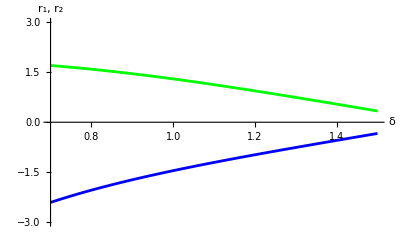

```mathematica
r1=-Simplify[1/f1(2(Ni^2-1)DS1 DS2)/(2 DS1^2(Ni+1)+DS2^3 Ni(Ni-1))/.{α->0.3,Ni->1.5187228,M->3}];
r2=Simplify[1/f1(2(Ni^2-1)DS1 DS2)/(2 DS1^2(Ni+1)-DS2^3 Ni(Ni-1))/.{α->0.3,Ni->1.5187228,M->3}];
Plot[{r1,r2},{δ,0.7,1.5},PlotStyle->{Green, Blue},AxesLabel->{"δ","r_1, r_2"},PlotRange->{-3,3}]
```

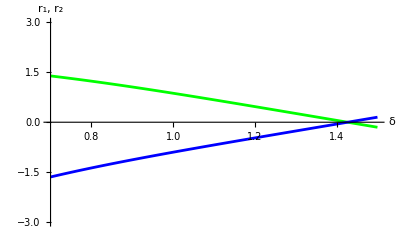

```mathematica
r1=-Simplify[1/f1(2(Ni^2-1)DS1 DS2)/(2 DS1^2(Ni+1)+DS2^3 Ni(Ni-1))/.{α->0.3,Ni->1.5187228,M->4}];
r2=Simplify[1/f1(2(Ni^2-1)DS1 DS2)/(2 DS1^2(Ni+1)-DS2^3 Ni(Ni-1))/.{α->0.3,Ni->1.5187228,M->4}];
Plot[{r1,r2},{δ,0.7,1.5},PlotStyle->{Green,Blue},AxesLabel->{"δ","r_1, r_2"},PlotRange->{-3,3}]
```

The above plots show that the best values of r_1 and r_2, i. e. the greatest absolute values which reduce higher order aberrations, are obtained for δ ϵ [0.7, 1] . Moreover, to obtain a lower obstruction, we must increase the magnification M. As a consequence, the radii r_1 and r_2 reduce and the higher-order aberrations increase.
These results are valid provided that the thickness of lenses can be neglected.

************************************************

************************************************

If the curvature radii are different, the following system has to be considered:

```mathematica
rad={1/c1,1/c2,1/c3,1/(c1-c2+c3)}; 
thick={0,0,0};
ind={{1,Ni,1,Ni,1}};
costasf={0,0,0,0};
TotalAberrations[rad,thick,ind,costasf,r,0,0,-Infinity,x,θ,{λ},0]
Null
```

Spherical coefficient

((c1-c2) (c2-c3) (-1+Ni) (-c3 (2+Ni)-2 c2 (-1+Ni^2)+c1 (-4-Ni+2 Ni^2)))/(8 Ni)

Coma coefficient

-((c1-c2) (c2-c3) (-1+Ni^2))/(2 Ni)

Astigmatism coefficient = 0

```mathematica
DC1=Simplify[Seidsphe[1]];
DC2=Simplify[Seidcoma[1]];
```

To put DC1 in a more convenient form, we note that the factor

1/(8 Ni)((-1+Ni) (-c3 (2+Ni)-2 c2 (-1+Ni^2)+c1 (-4-Ni+2 Ni^2)))

becomes

```mathematica
Apart[Simplify[Expand[1/(8 Ni)((-1+Ni) (-c3 (2+Ni)-2 c2 (-1+Ni^2)+c1 (-4-Ni+2 Ni^2)))]]]
```

1/8 (-3 c1+2 c2-c3)+(2 c1-c2+c3)/(4 Ni)-1/8 (3 c1-2 c2+c3) Ni+1/4 (c1-c2) Ni^2

Spherical aberration and coma coefficients of C write:

D1C = (c_2-c_3)(c_1-c_2)(-(Ni+1)/8(3 c_1-2 c_2+c_3)+
1/(4Ni)(2 c_1-c_2+c_3)+Ni^2/4(c_1-c_2)),

D2C = -(Ni^2-1)/(2Ni)(c_1-c_2)(c_2-c_3).

The curvature radii

 R_1=1/c_1, R_2=1/c_2, R_3=1/c_3, R_4=1/(c_1-c_2+c_3) 

of the two lenses of C, which eliminate spherical aberration and coma verify the system

D1S + D1C = 0,
D2S + D2C = 0.

In Chapter 4 it is proved that this system is equivalent to the following second degree system

a_1 x+a_2 y=d_1,
(x-y)(y-1)=d_2,

where x=c_1/c_3=R_3/R_1, y=c_2/c_3=R_3/R_2 and 

a_1=1/(8Ni)(4-3Ni-3 Ni^2+2 Ni^3),
a_2=1/(4Ni)(-1+Ni+Ni^2-Ni^3),
d_1=1/8-1/(4Ni)+Ni/8-((Ni^2-1)R_3 DS1)/(2Ni DS2),         (2)
d_2=(2 NiR_3^2 DS2)/(Ni^2-1).


The solutions of the above system write:

```mathematica
eq1=a1 x+a2 y==d1;
eq2=(x-y)(y-1)==d2;
Solve[{eq1,eq2},{x,y}]//Simplify
Null
```

{{x→(-a1 a2-a2^2+2 a1 d1+a2 d1+a2 √((a1+a2+d1)^2-4 (a1+a2) (d1+a1 d2)))/(2 a1 (a1+a2)),y→(a1+a2+d1-√((a1+a2+d1)^2-4 (a1+a2) (d1+a1 d2)))/(2 (a1+a2))},{x→-(a1 a2+a2^2-2 a1 d1-a2 d1+a2 √((a1+a2+d1)^2-4 (a1+a2) (d1+a1 d2)))/(2 a1 (a1+a2)),y→(a1+a2+d1+√((a1+a2+d1)^2-4 (a1+a2) (d1+a1 d2)))/(2 (a1+a2))}}

Finally, recalling that

x=c_1/c_3=R_3/R_1, y=c_2/c_3=R_3/R_2

and introducing the nondimensional radii

r_1=R_1/f,  r_2=R_2/f,  r_3=R_3/f,  r_4=R_4/f,

the following two solutions are obtained:

r_1=-r_3(2a_1(a_1+a_2))/(a_1(a_2-2 d_1)+a_2(a_2-d_1+√Δ)),
r_2=    r_3(2(a_1+a_2))/(a_1+a_2+d_1+√Δ),                                   (3)

r_1= r_3(2a_1(a_1+a_2))/(-a_1(a_2-2 d_1)+a_2(-a_2+d_1+√Δ))
r_2= r_3(2(a_1+a_2))/(a_1+a_2+d_1-√Δ),                                       (4)  

where

Δ =(a_1+a_2+d_1)^2-4(a_1+a_2)(d_1+a_1 d_2).        (5)

These solutions are real if Δ>0. Owing to (2), the radii (3)-(4) and Δ, are functions of r_3  and  δ.To find the region of the plane (r_3, δ) in which Δ>0, for the glass BK7 (Ni = 1.5187228, in green light), it is sufficient to resort to the command InequalityGraphics of Mathematica.

```mathematica
sost={a1->(4-3 Ni-3 Ni^2+2 Ni^3)/(8 Ni),a2->(-1+Ni+Ni^2-Ni^3)/(4 Ni),d1->1/8-1/(4 Ni)+Ni/8-((Ni^2-1)f1 r3 DS1)/(2 Ni DS2),d2->(2Ni r3^2 f1^2 DS2)/(Ni^2-1)}/.{α->0.4,Ni->1.5187228,M->4};
Δ=((a1+a2+d1)^2-4 (a1+a2) (d1+a1 d2))/.sost;
```

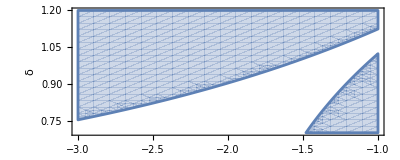

```mathematica
RegionPlot[Simplify[Δ>0],{r3,-3,-1},{δ,0.7,1.2},AspectRatio->0.4,AxesLabel->{"r_3","δ"}]
```

It is very important to recognize the behaviour of the radii (1)-(2) on varying r_3 in the interval of its acceptable values for any fixed δ.
The analysis of plots r_1, r_2 versus r_3, corresponding to both solutions, show that their more convenient values, for a fixed δ, are obtained for δ∈(0.7,1.1) and r_3 coinciding with the lower bound of the interval determined by the intersection of the stright line δ = const with the region on the right hand side of the previous figure.

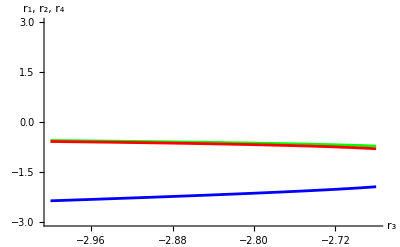

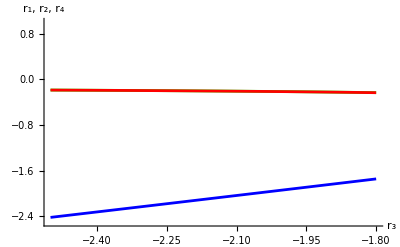

```mathematica
r11=(-r3(2 a1 (a1+a2))/(a1 (a2-2 d1)+a2 (a2-d1+√Δ)))/.sost;
r21=(r3 (2 (a1+a2))/(a1+a2+d1+√Δ))/.sost;
r41=(r11 r21 r3)/(r21 r3-r11 r3+r11 r21);
Plot[{r11/.δ->0.8,r21/.δ->0.8,r41/.δ->0.8},{r3,-3,-2.68},PlotStyle->{Green,Blue,Red},PlotRange->{-3,3},AxesLabel->{"r_3","r_1, r_2, r_4"}]
Plot[{r11/.δ->1.1,r21/.δ->1.1,r41/.δ->1.1},{r3,-2.5,-1.8},PlotStyle->{Green,Blue,Red},PlotRange->{-2.5,1},AxesLabel->{"r_3","r_1, r_2, r_4"}]
```

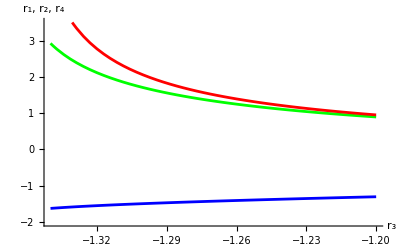

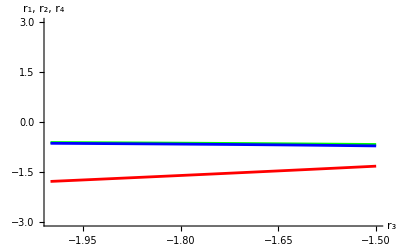

```mathematica
r12=(r3(2 a1 (a1+a2))/(-a1 (a2-2 d1)+a2 (-a2+d1+√Δ)))/.sost;
r22=(r3 (2 (a1+a2))/(a1+a2+d1-√Δ))/.sost;
r42=(r12 r22 r3)/(r22 r3-r12 r3+r12 r22);
Plot[{r12/.δ->0.8,r22/.δ->0.8,r42/.δ->0.8},{r3,-1.34,-1.2},PlotStyle->{Green,Blue,Red},PlotRange->{-2,3.5},AxesLabel->{"r_3","r_1, r_2, r_4"}]
Plot[{r12/.δ->1.1,r22/.δ->1.1,r42/.δ->1.1},{r3,-2,-1.5},PlotStyle->{Green,Blue,Red},PlotRange->{-3,3},AxesLabel->{"r_3","r_1, r_2, r_4"}]
```

The above plots show that the best values of r_1, r_2 and r_3, i. e. the greatest absolute values which reduce higher-order aberrations, are given by the second solution and for δ ϵ [0.7, 0.9] . Moreover, to reduce the obstruction, we must increase the magnification M. As a consequence, the radii r_1 and r_2 reduce and the higher-order aberrations increase.
These results are valid provided that the thickness of lenses can be neglected.

************************************************

************************************************

If we wish to control the astigmatism in a Houghton's combination, a secondary mirror S_2, with a conic constant K, has to be used. In fact, to evaluate the aberrations of S_1, S_2, with the aperture stop A at a distance δ in front of S_1, we consider the system

```mathematica
rad={Infinity,Infinity,-2f1,γ f1}; 
thick={0,δ f1,-β f1};
ind={1,1,1,-1,1}; 
costasf={0,0,K1,0};
NTAberrations[rad,thick,ind,costasf,r,θ]
DS1p=Simplify[Absfer]
DS2p=Simplify[Comatot]
DS3p=Simplify[Asttot]
Null
```

NTAberrations[{∞,∞,-2 f1,(2 f1 M (1+α))/(1-M^2)},{0,f1 δ,-(f1 (M-α))/(1+M)},{1,1,1,-1,1},{0,0,K1,0},r,θ]

Absfer

Comatot

Asttot

```mathematica
rad={Infinity,Infinity,-2f1,γ f1}; 
thick={0,δ f1,-β f1};
ind={1,1,1,-1,1}; 
costasf={0,0,0,K2};
NTAberrations[rad,thick,ind,costasf,r,θ]
DS1s=Simplify[Absfer]
DS2s=Simplify[Comatot]
DS3s=Simplify[Asttot]
Null
```

NTAberrations[{∞,∞,-2 f1,(2 f1 M (1+α))/(1-M^2)},{0,f1 δ,-(f1 (M-α))/(1+M)},{1,1,1,-1,1},{0,0,0,K2},r,θ]

Absfer

Comatot

Asttot

Consequently, the astigmatism vanishes when

```mathematica
conicp=Flatten[Solve[DS3p==0,K1]//Simplify]
conics=Flatten[Solve[DS3s==0,K2]//Simplify]
```

{}

{}

and the spherical aberration and coma coefficients of S write:

```mathematica
DS1pf=Simplify[DS1p/.conicp]
DS2pf=Simplify[DS2p/.conicp]
DS1sf=Simplify[DS1s/.conics]
DS2sf=Simplify[DS2s/.conics]
Null
```

Absfer

Comatot

Absfer

Comatot

Substituting these expressions into (*), one obtains:

```mathematica
R1p=-Simplify[(2(Ni^2-1)DS1pf DS2pf)/(2 DS1pf^2(Ni+1)+DS2pf^3 Ni(Ni-1))];
R2p=Simplify[(2(Ni^2-1)DS1pf DS2pf)/(2 DS1pf^2(Ni+1)-DS2pf^3 Ni(Ni-1))];

R1s=-Simplify[(2(Ni^2-1)DS1sf DS2sf)/(2 DS1sf^2(Ni+1)+DS2sf^3 Ni(Ni-1))];
R2s=Simplify[(2(Ni^2-1)DS1sf DS2sf)/(2 DS1sf^2(Ni+1)-DS2sf^3 Ni(Ni-1))];
```

To recognize the behavior of the radii on varying δ, we introduce the nondimensional radii:

```mathematica
sost1={α->0.4,Ni->1.5187228,M->4};
r1p=(R1p/f1)/.sost1;
r2p=(R2p/f1)/.sost1;
k1=conicp[[1,2]]/.sost1;
r1s=(R1s/f1)/.sost1;
r2s=(R2s/f1)/.sost1;
k2=conics[[1,2]]/.sost1;
```

Part::partw: Part 1 of {} does not exist.

and resorting to the plot (r_1, r_2, K) versus δ, the behavior of K, r_1  and  r_2 on varying δ can be recognized.

```mathematica
Plot[{r1p,r2p,k1},{δ,1,1.2},PlotStyle->{GrayLevel[0],Dashing[{.03}],Dashing[{0.01}]}, AxesLabel->{"δ","(r_1,r_2,K1) "},PlotRange->{-1,1}]
Plot[{r1s,r2s,k2},{δ,0.7,1},PlotStyle->{GrayLevel[0],Dashing[{.03}],Dashing[{0.01}]}, AxesLabel->{"δ","(r_1,r_2,K1) "},PlotRange->{-1.5,1.5}]
Null
```

-Graphics-

-Graphics-

The more convenient values are obtained for δ ϵ [1.2, 1.4].

# Summary

Symmetric doublet 


R_1=f(4(Ni^2-1)(2-δ))/((Ni+1)+Ni(Ni-1)(2-δ)^3),          
R_2=-f(4(Ni^2-1)(2-δ))/((Ni+1)-Ni(Ni-1)(2-δ)^3),

δ ϵ [0.75, 1]. This is a good combination for speed less than F/3.5


Doublet with different radii (no control on astigmatism)
 
r_1=-r_3(2a_1(a_1+a_2))/(a_1(a_2-2 d_1)+a_2(a_2-d_1+√Δ)),
r_2=    r_3(2(a_1+a_2))/(a_1+a_2+d_1+√Δ),                                   

r_1= r_3(2a_1(a_1+a_2))/(-a_1(a_2-2 d_1)+a_2(-a_2+d_1+√Δ))
r_2= r_3(2(a_1+a_2))/(a_1+a_2+d_1-√Δ),                                         

where

Δ =(a_1+a_2+d_1)^2-4(a_1+a_2)(d_1+a_1 d_2)>0.        

δ ϵ [0.8, 1.2]. This is a good combination for speed less than F/2.5

# HCassegrain1

Input data:
f1      = primary focal;
ft     = total focal;
spes = thickness list of corrector and its distance from primary mirror;
em   = back focal;
diam = diameter of corrector;
angle      = field angle;
waves = wave lengths considered;
sf = to balance spherical aberration
co = to balance coma
cr = to balance chromatism;

```mathematica
HCassegrain1[f1_,ft_,spes_,em_,diam_,ind_,angle_,waves_,sf_,co_,cr_]:=
Module[{α,M,β,γ,A,B,AS,r11,r12,sol1,ra1,pl},
Ni=ind[[1,2]];
α=em/f1;
δ=spes[[4]]/f1;
M=ft/ f1;
β=(M-α)/(M+1);
γ=(2M(1+α))/(1-M^2);

A=-1/(32 f1^3)+((α+1) (-1+M^2))/(32 f1^3 M^3);
B=(α(1-M^2)+M (1+M^2))/(8 f1^2 M^3)-((1-M^2+M^3+α-M^2 α) δ)/(8 f1^2 M^3);
AS=(M^4-2 M α-α^2-2 M^3 (2+α)+M^2 (-1+α^2))/(8 f1 M^3 (1+α))+((M+M^3+α-M^2 α) δ)/(4 f1 M^3)-((1+M^3+α-M^2 (1+α)) δ^2)/(8 f1 M^3);
r11=(2 A B (-1+Ni) (1+Ni))/(-2 A^2-2 A^2 Ni+B^3 Ni-B^3 Ni^2);
r12=(2 A B (-1+Ni^2))/(2 A^2+2 A^2 Ni+B^3 Ni-B^3 Ni^2);

thick=Join[spes,{-β f1}];

TotalAberrations[{1/c11,1/c12,-1/c11,1/c13,1/c15,γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
so1=FindRoot[{Absftot[1]==0,Comatot[1]==0,zog1[2,n]-zog1[3,n]==0,foc[1]==ft},{c11,1/r11},{c12,1/r12},{c13,-1/r12},{c15,-1/(2f1)}];
sf3=Absftot[1];
co3=Comatot[1];
axcr=zog1[2,n]-zog1[3,n];

HOrdAberrations[{1/so1[[1,2]],1/so1[[2,2]],-1/so1[[1,2]],1/so1[[3,2]],1/so1[[4,2]],γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
sf5=sfer5;
co5=coma5;

MarginalRayTracing[{1/so1[[1,2]],1/so1[[2,2]],-1/so1[[1,2]],1/so1[[3,2]],1/so1[[4,2]],γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
margcr=znu[2]-znu[3];

TotalAberrations[{1/c21,1/c22,-1/c21,1/c23,1/c25,γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
so2=FindRoot[{Absftot[1]==-sf sf5,Comatot[1]==-co co5,zog1[2,n]-zog1[3,n]==-cr margcr,foc[1]==ft},{c21,so1[[1,2]]},{c22,so1[[2,2]]},{c23,so1[[3,2]]},{c25,so1[[4,2]]}];

TotalAberrations[{1/so2[[1,2]],1/so2[[2,2]],-1/so2[[1,2]],1/so2[[3,2]],1/so2[[4,2]],γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
sf31=Absftot[1];
co31=Comatot[1];
HOrdAberrations[{1/so2[[1,2]],1/so2[[2,2]],-1/so2[[1,2]],1/so2[[3,2]],1/so2[[4,2]],γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
sf51=sfer5;
co51=coma5;

MarginalRayTracing[{1/so2[[1,2]],1/so2[[2,2]],-1/so2[[1,2]],1/so2[[3,2]],1/so2[[4,2]],γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
AxialChr=zog1[2,n]-zog1[3,n];
margcr1=znu[2]-znu[3];


Print["The final radii of Houghton's doublet are:"];
Print["r1 = ",1/so2[[1,2]]];
Print["r2 = ",1/so2[[2,2]]];
Print["r3 = ",-1/so2[[1,2]]];
Print["r4 = ",1/so2[[3,2]]];
Print["Primary radius = ",1/so2[[4,2]]];
Print["Secondary radius = ",γ f1];
Print["Distanza of secondary from primary = ",-β f1];
Print["Obstruction coefficient = ",1-β];
Print["Focal length = ",foc[1]];
Print["Height of the object = ",hobj1[1,n]];
Print["Third-order spherical aberration = ",sf31];
Print["Fifth-order spherical aberration = ",sf51];
Print["Third-order coma = ",co31];
Print["Fifth-order coma = ",co51];
Print["Third-order astigmatism = ",Asttot[1]];
Print["Marginal chromatism = ",margcr1];
Print["AxialChr = ",AxialChr];




spess11[1]=0;
Do[
spess11[i]=Sum[thick[[j]],{j,1,i-1}],
{i,2,n}];
ra11={r1,r2,r3d,r4};

Do[
Which[ra11[[j]]>0,fu[j]=ra11[[j]]+spess11[j]-√(ra11[[j]]^2-x^2),ra11[[j]]<0,fu[j]=ra11[[j]]+spess11[j]+√(ra11[[j]]^2-x^2)];

pl[j]=Plot[fu[j],{x,-diam/2,diam/2},PlotStyle->{Red,Blue}],
{j,1,4}];
ta=Table[fu[j],{j,1,4}];
Print[Plot[ta,{x,-diam/2,diam/2},PlotStyle->{Red,Red,Blue,Blue},AspectRatio->1/5]];

]
```

The final radii of Houghton's doublet are:

r1 = 818.87

r2 = -943.312

r3 = -818.87

r4 = 929.687

Primary radius = -1198.63

Secondary radius = -471.429

Distanza of secondary from primary = -428.571

Obstruction coefficient = 0.285714

Focal length = 2200.

Height of the object = 8.44739

Third-order spherical aberration = -0.0421709

Fifth-order spherical aberration = 0.0418368

Third-order coma = 0.000524869

Fifth-order coma = -0.00052639

Third-order astigmatism = 0.000144868

Marginal chromatism = 0.0804341

AxialChr = -0.438129

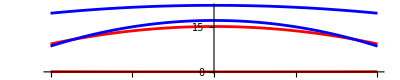

```mathematica
(*2200-200F/3.5 *)
f1=600;
ft=2200.;
spes={15,2,5,490};
em=200;
diam=200;
angle=0.22;
ind={{1,1.5187228,1,1.5187228,1,-1,1},{1,1.522376,1,1.522376,1,-1,1},{1,1.514322,1,1.514322,1,-1,1}};
waves={λ1,λ2,λ3};
sf=1.03;
co=0.97;
cr=0.8;
HCassegrain1[f1,ft,spes,em,diam,ind,angle,waves,sf,co,cr]
```

# HCassegrain2

Input data:
f1     = primary focal;
ft     = total focal;
spes = thickness list of corrector and its distance from primary mirror;
em   = back focal;
diam = diameter of corrector;
ind    = list of refractive indices;
angle = field angle;
waves = wave lengths considered;
sf = to balance spherical aberration
co = to balance coma
cr = to balance chromatism;

```mathematica
HCassegrain2[f1_,ft_,em_,spes_,diam_,ind_,angle_,waves_,sf_,co_,cr_]:=
Module[{(*α,M,β,γ,A,B,AS,a1,a2,D1,D2,r1,r2,r3,r4,r3d,ra11,pl*)},
Ni=ind[[1,2]];
α=em/f1;
δ=spes[[4]]/f1;

M=ft/ f1;
β=(M-α)/(M+1);
γ=(2M(1+α))/(1-M^2);
A=-1/(32 f1^3)+((α+1) (-1+M^2))/(32 f1^3 M^3);
B=(α(1-M^2)+M (1+M^2))/(8 f1^2 M^3)-((1-M^2+M^3+α-M^2 α) δ)/(8 f1^2 M^3);
AS=(M^4-2 M α-α^2-2 M^3 (2+α)+M^2 (-1+α^2))/(8 f1 M^3 (1+α))+((M+M^3+α-M^2 α) δ)/(4 f1 M^3)-((1+M^3+α-M^2 (1+α)) δ^2)/(8 f1 M^3);
a11=(4-3 Ni-3 Ni^2+2 Ni^3)/(8 Ni);
a21=(-1+Ni+Ni^2-Ni^3)/(4 Ni);
D1=1/8-1/(4 Ni)+Ni/8-((-1+Ni^2) ra3 f1 A)/(2 Ni B);
D2=(2Ni)/(Ni^2-1)B*ra3^2 f1^2;
Δ=(a11+a21+D1)^2-4 (a11+a21) (D1+a11 D2);

Δ1=Numerator[Simplify[Δ]];

sr=Flatten[Solve[Δ1==0,ra3]//Sort];

rd[2]=0.99sr[[2,2]];

(* Second solution *)
r1=-f1 ra3(2 a11 (a11+a21))/(a11 (a21-2 D1)+a21 (a21-D1+√Δ))/.ra3->rd[2];
r2=f1 ra3 (2 (a11+a21))/(a11+a21+D1+√Δ)/.ra3-> rd[2];
r3d=f1 rd[2];
r4=( r1 r2 r3d)/ (r1 (r2-r3d)+r2 r3d); 
thick=Join[spes,{-β f1}];

TotalAberrations[{1/c11,1/c12,r3d,1/c14,1/c15,γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
so1=FindRoot[{Absftot[1]==0,Comatot[1]==0,zog1[2,n]-zog1[3,n]==0,foc[1]==ft},{c11,1/r1},{c12,1/r2},{c14,1/r4},{c15,-1/(2f1)}];

HOrdAberrations[{1/so1[[1,2]],1/so1[[2,2]],r3d,1/so1[[3,2]],1/so1[[4,2]],γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];

sf5=sfer5;
co5=coma5;

MarginalRayTracing[{1/so1[[1,2]],1/so1[[2,2]],r3d,1/so1[[3,2]],1/so1[[4,2]],γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
margcr=znu[2]-znu[3];

TotalAberrations[{1/c21,1/c22,r3d,1/c24,1/c25,γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
so2=FindRoot[{Absftot[1]==-sf sf5,Comatot[1]==-co co5,zog1[2,n]-zog1[3,n]==-cr margcr,foc[1]==ft},{c21,so1[[1,2]]},{c22,so1[[2,2]]},{c24,so1[[3,2]]},{c25,so1[[4,2]]}];

TotalAberrations[{1/so2[[1,2]],1/so2[[2,2]],r3d,1/so2[[3,2]],1/so2[[4,2]],γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
axcr1=zog1[2,n]-zog1[3,n];
sf31=Absftot[1];
co31=Comatot[1];
HOrdAberrations[{1/so2[[1,2]],1/so2[[2,2]],r3d,1/so2[[3,2]],1/so2[[4,2]],γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
sf51=sfer5;
co51=coma5;

MarginalRayTracing[{1/so2[[1,2]],1/so2[[2,2]],r3d,1/so2[[3,2]],1/so2[[4,2]],γ f1},thick,ind,{0,0,0,0,0,0},diam/2,0,0,-Infinity,y,angle,waves,2];
margcr1=znu[2]-znu[3];


Print["The final radii of Houghton's doublet are:"];
Print["r1 = ",1/so2[[1,2]]];
Print["r2 = ",1/so2[[2,2]]];
Print["r3 = ",r3d];
Print["r4 = ",1/so2[[3,2]]];
Print["Primary radius = ",1/so2[[4,2]]];
Print["Secondary radius = ",γ f1];
Print["Distanza of secondary from primary = ",-β f1];
Print["Obstruction coefficient = ",1-β];
Print["Focal length = ",foc[1]];
Print["Height of the object = ",hobj1[1,n]];
Print["Third-order spherical aberration = ",sf31];
Print["Fifth-order spherical aberration = ",sf51];
Print["Third-order coma = ",co31];
Print["Fifth-order coma = ",co51];
Print["Third-order astigmatism = ",Asttot[1]];
Print["Axial chromatism = ",axcr1];
Print["Marginal chromatism = ",margcr1];


spess11[1]=0;
Do[
spess11[i]=Sum[thick[[j]],{j,1,i-1}],
{i,2,n}];
ra11={r1,r2,r3d,r4};

Do[
Which[ra11[[j]]>0,fu[j]=ra11[[j]]+spess11[j]-√(ra11[[j]]^2-x^2),ra11[[j]]<0,fu[j]=ra11[[j]]+spess11[j]+√(ra11[[j]]^2-x^2)];

pl[j]=Plot[fu[j],{x,-diam/2,diam/2},PlotStyle->{Red,Blue}],
{j,1,4}];
ta=Table[fu[j],{j,1,4}];
Print[Plot[ta,{x,-diam/2,diam/2},PlotStyle->{Red,Red,Blue,Blue},AspectRatio->1/5]];



]
```

```mathematica
(*2400-200F/3 *)
f1=600;
ft=2400.;
spes={15,5,5,460};
em=200;
diam=200;
ind={{1,1.5187228,1,1.5187228,1,-1,1},{1,1.522376,1,1.522376,1,-1,1},{1,1.514322,1,1.514322,1,-1,1}};
angle=0.27;
waves={λ1,λ2,λ3};
sf=1.2;
co=1;
cr=0.8;
HCassegrain2[f1,ft,em,spes,diam,ind,angle,waves,sf,co,cr]
```

HCassegrain2[600,2400.,200,{15,5,5,460},200,{{1,1.51872,1,1.51872,1,-1,1},{1,1.52238,1,1.52238,1,-1,1},{1,1.51432,1,1.51432,1,-1,1}},0.27,{λ1,λ2,λ3},1.2,1,0.8]

The final radii of Houghton's doublet are:

r1 = 5033.52

r2 = -1086.78

r3 = -709.429

r4 = -3481.03

Primary radius = -1000.5

Secondary radius = -373.333

Distanza of secondary from primary = -360.

Obstruction coefficient = 0.28

Focal length = 2000.

Height of the object = 10.472

Third-order spherical aberration = -0.0178855

Fifth-order spherical aberration = 0.0177548

Third-order coma = 0.00085579

Fifth-order coma = -0.000859089

Third-order astigmatism = 0.000375473

Axial chromatism = -0.406206

Marginal chromatism = 0.0956866

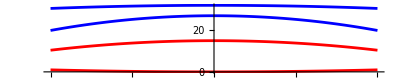

```mathematica
(*2000-200F/2.5 *)
f1=500;
ft=2000.;
spes={15,12,5,370};
em=200;
diam=200;
ind={{1,1.5187228,1,1.5187228,1,-1,1},{1,1.522376,1,1.522376,1,-1,1},{1,1.514322,1,1.514322,1,-1,1}};
angle=0.3;
waves={λ1,λ2,λ3};
sf=1.08;
co=0.97;
cr=0.8;
HCassegrain2[f1,ft,em,spes,diam,ind,angle,waves,sf,co,cr]
```

The final radii of Houghton's doublet are:

r1 = 80930.9

r2 = -869.248

r3 = -593.041

r4 = -1933.05

Primary radius = -900.446

Secondary radius = -308.097

Distanza of secondary from primary = -330.612

Obstruction coefficient = 0.265306

Focal length = 2000.

Height of the object = 10.472

Third-order spherical aberration = -0.0370793

Fifth-order spherical aberration = 0.0369732

Third-order coma = 0.00158971

Fifth-order coma = -0.00155522

Third-order astigmatism = 0.000813841

Axial chromatism = -0.504114

Marginal chromatism = 0.157678

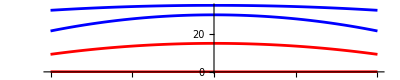

```mathematica
(*2000-200F/2.25 *)
f1=450;
ft=2000.;
spes={15,15,5,340};
em=200;
diam=200;
ind={{1,1.5187228,1,1.5187228,1,-1,1},{1,1.522376,1,1.522376,1,-1,1},{1,1.514322,1,1.514322,1,-1,1}};
angle=0.3;
waves={λ1,λ2,λ3};
sf=1.08;
co=0.97;
cr=0.75;
HCassegrain2[f1,ft,em,spes,diam,ind,angle,waves,sf,co,cr]
```